This notebook provides an example of how to use the packages Fermat.m and psi.m, which compute numerical approximations to the Ricci-flat metric on the Calabi-Yau manifold defined by the polynomial

∑_a (z^a)^(N+1)+(N+1)ψ∏_a z^a

in $CP^N$. These packages follow the strategy and methods described in the paper "Energy functionals for Calabi-Yau metrics" by M. Headrick and A. Nassar (arXiv: 0908.2635 [hep-th]). The package Fermat.m is for the case ψ==0, while the package psi.m is for the case of real non-zero ψ.

Before loading the package, you set the values of the variables N1, which is N+1 (i.e. 3 for T^2, 4 for K3, 5 for the quintic), and k. For psi.m you also define ps, which should be a real number. Here we will consider the Fermat example. You should also set the directory where the package is located. For example:

```mathematica
N1=4;
k=6;
SetDirectory["CY energy/packages"]
```

/Volumes/mpheadrick/work/CY energy/packages

When the package is loaded, it computes the basis of degree (k,k) polynomials.

```mathematica
<<Fermat.m
```

Basis of polynomials computed. The space is 10 dimensional.

The function sprinkle sprinkles points on the manifold. The first argument is the number of points to sprinkle, N_points), the second is the tolerance ϵ. For most purposes, 1000 points and a tolerance of ϵ==0.1 should be quite adequate. With these values, the process should take a few seconds.

```mathematica
points1=sprinkle[1000,0.1];
```

We then have to calculate, for each point, the values of the vector Q_a and the matrix Ψ for each polynomial in the basis. For low values of k like this one, this takes less than a second:

```mathematica
data1=calcData[points1];
```

For larger set of points and larger values of N1 and k, this step can take considerably longer (minutes or hours). Therefore, we have provided functions to store and retrieve the data in binary form (using >> and << would result in text files, which are much larger than binary):

```mathematica
storeData[data1,"data1"]
```

data1

```mathematica
data2=getData["data1"];
```

```mathematica
data1==data2
```

True

An algebraic metric is represented as a list of real numbers, the coefficients of the basis polynomials. In this case (with N==3 and k==6) we saw that the vector space of polynomials is 10-dimensional, so the number of coefficients is 9. The Fubini-Study metric is gFS:

```mathematica
gFS
```

{459.,204.,153.,612.,-19.89,56.61,51.,61.6,21.42}

The function EE evaluates the functional E, on a given algebraic metric using a given set of points (for this and other functions, you will get slightly different results from those shown here, since you will have a different sample of points):

```mathematica
EE[gFS,data1]
```

0.0949976

The full list of values of η is obtained using eta:

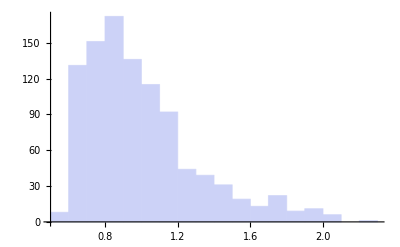

```mathematica
Histogram[eta[gFS,data1]]
```

The function minimize uses Mathematica's built-in FindMinimum routine with the method set to Levenberg-Marquardt, starting from any given algebraic metric. This process takes a few seconds.

```mathematica
gmin=minimize[gFS,data1]
```

{101.156,63.0379,44.6675,226.825,-8.20719,30.4195,26.9831,41.19,9.33181}

```mathematica
EE[gmin,data1]
```

4.93294×10^-8

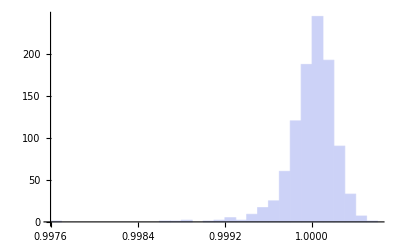

```mathematica
Histogram[eta[gmin,data1]]
```

Does the value of E found really represent the minimum? In other words, have we used enough points to accurately find the minimum? To test this, we pick an independent set of 1000 points, and evaluate E at the putative minimum using those points:

```mathematica
data3=calcData[sprinkle[1000,0.1]];
```

```mathematica
EE[gmin,data3]
```

5.66178×10^-8

The answer is quite close to the value found using the original set of points.

The polynomial p (entering into the Kaehler potential) can be obtained using the function p:

```mathematica
p[gmin]
```

101.156 (8 u_1^2 u_2 u_3 (ū)_1^2 (ū)_2 (ū)_3+8 u_1 u_2^2 u_3 (ū)_1 (ū)_2^2 (ū)_3+8 u_1^2 u_2^2 u_3 (ū)_1^2 (ū)_2^2 (ū)_3+8 u_1 u_2 u_3^2 (ū)_1 (ū)_2 (ū)_3^2+8 u_1^2 u_2 u_3^2 (ū)_1^2 (ū)_2 (ū)_3^2+8 u_1 u_2^2 u_3^2 (ū)_1 (ū)_2^2 (ū)_3^2)+44.6675 (12 u_1^2 u_2^2 (ū)_1^2 (ū)_2^2+12 u_1^2 u_3^2 (ū)_1^2 (ū)_3^2+12 u_2^2 u_3^2 (ū)_2^2 (ū)_3^2+12 u_1^2 u_2^2 u_3^2 (ū)_1^2 (ū)_2^2 (ū)_3^2)+63.0379 (12 u_1 u_2 u_3 (ū)_1 (ū)_2 (ū)_3+12 u_1^3 u_2 u_3 (ū)_1^3 (ū)_2 (ū)_3+12 u_1 u_2^3 u_3 (ū)_1 (ū)_2^3 (ū)_3+12 u_1 u_2 u_3^3 (ū)_1 (ū)_2 (ū)_3^3)+226.825 (2 u_1^2 u_2 (ū)_1^2 (ū)_2+2 u_1^3 u_2 (ū)_1^3 (ū)_2+2 u_1 u_2^2 (ū)_1 (ū)_2^2+2 u_1^3 u_2^2 (ū)_1^3 (ū)_2^2+2 u_1 u_2^3 (ū)_1 (ū)_2^3+2 u_1^2 u_2^3 (ū)_1^2 (ū)_2^3+2 u_1^2 u_3 (ū)_1^2 (ū)_3+2 u_1^3 u_3 (ū)_1^3 (ū)_3+2 u_2^2 u_3 (ū)_2^2 (ū)_3+2 u_1^3 u_2^2 u_3 (ū)_1^3 (ū)_2^2 (ū)_3+2 u_2^3 u_3 (ū)_2^3 (ū)_3+2 u_1^2 u_2^3 u_3 (ū)_1^2 (ū)_2^3 (ū)_3+2 u_1 u_3^2 (ū)_1 (ū)_3^2+2 u_1^3 u_3^2 (ū)_1^3 (ū)_3^2+2 u_2 u_3^2 (ū)_2 (ū)_3^2+2 u_1^3 u_2 u_3^2 (ū)_1^3 (ū)_2 (ū)_3^2+2 u_2^3 u_3^2 (ū)_2^3 (ū)_3^2+2 u_1 u_2^3 u_3^2 (ū)_1 (ū)_2^3 (ū)_3^2+2 u_1 u_3^3 (ū)_1 (ū)_3^3+2 u_1^2 u_3^3 (ū)_1^2 (ū)_3^3+2 u_2 u_3^3 (ū)_2 (ū)_3^3+2 u_1^2 u_2 u_3^3 (ū)_1^2 (ū)_2 (ū)_3^3+2 u_2^2 u_3^3 (ū)_2^2 (ū)_3^3+2 u_1 u_2^2 u_3^3 (ū)_1 (ū)_2^2 (ū)_3^3)+26.9831 (8 u_1^3 (ū)_1^3+8 u_2^3 (ū)_2^3+8 u_1^3 u_2^3 (ū)_1^3 (ū)_2^3+8 u_3^3 (ū)_3^3+8 u_1^3 u_3^3 (ū)_1^3 (ū)_3^3+8 u_2^3 u_3^3 (ū)_2^3 (ū)_3^3)-16.4144 (4 u_1 u_2 u_3^4 (ū)_1 (ū)_2+4 u_2 u_3^4 (ū)_1^4 (ū)_2+4 u_1 u_3^4 (ū)_1 (ū)_2^4+4 u_1 u_2^4 u_3 (ū)_1 (ū)_3+4 u_2^4 u_3 (ū)_1^4 (ū)_3+4 u_1^4 u_2 u_3 (ū)_2 (ū)_3+4 u_2 u_3 (ū)_1^4 (ū)_2 (ū)_3+4 u_1^4 u_3 (ū)_2^4 (ū)_3+4 u_1 u_3 (ū)_1 (ū)_2^4 (ū)_3+4 u_1 u_2^4 (ū)_1 (ū)_3^4+4 u_1^4 u_2 (ū)_2 (ū)_3^4+4 u_1 u_2 (ū)_1 (ū)_2 (ū)_3^4)+60.8389 (4 u_1 u_2 (ū)_1 (ū)_2+4 u_1^4 u_2 (ū)_1^4 (ū)_2+4 u_1 u_2^4 (ū)_1 (ū)_2^4+4 u_1 u_3 (ū)_1 (ū)_3+4 u_1^4 u_3 (ū)_1^4 (ū)_3+4 u_2 u_3 (ū)_2 (ū)_3+4 u_1^4 u_2 u_3 (ū)_1^4 (ū)_2 (ū)_3+4 u_2^4 u_3 (ū)_2^4 (ū)_3+4 u_1 u_2^4 u_3 (ū)_1 (ū)_2^4 (ū)_3+4 u_1 u_3^4 (ū)_1 (ū)_3^4+4 u_2 u_3^4 (ū)_2 (ū)_3^4+4 u_1 u_2 u_3^4 (ū)_1 (ū)_2 (ū)_3^4)-19.595 (2 u_1^2 u_2^4 (ū)_1^2+2 u_1^2 u_3^4 (ū)_1^2+2 u_2^4 (ū)_1^4+2 u_3^4 (ū)_1^4+2 u_1^4 u_2^2 (ū)_2^2+2 u_2^2 u_3^4 (ū)_2^2+2 u_2^2 (ū)_1^4 (ū)_2^2+2 u_2^2 u_3^4 (ū)_1^4 (ū)_2^2+2 u_1^4 (ū)_2^4+2 u_3^4 (ū)_2^4+2 u_1^2 (ū)_1^2 (ū)_2^4+2 u_1^2 u_3^4 (ū)_1^2 (ū)_2^4+2 u_1^4 u_3^2 (ū)_3^2+2 u_2^4 u_3^2 (ū)_3^2+2 u_3^2 (ū)_1^4 (ū)_3^2+2 u_2^4 u_3^2 (ū)_1^4 (ū)_3^2+2 u_3^2 (ū)_2^4 (ū)_3^2+2 u_1^4 u_3^2 (ū)_2^4 (ū)_3^2+2 u_1^4 (ū)_3^4+2 u_2^4 (ū)_3^4+2 u_1^2 (ū)_1^2 (ū)_3^4+2 u_1^2 u_2^4 (ū)_1^2 (ū)_3^4+2 u_2^2 (ū)_2^2 (ū)_3^4+2 u_1^4 u_2^2 (ū)_2^2 (ū)_3^4)+41.19 (4 u_1^2 (ū)_1^2+4 u_1^4 (ū)_1^4+4 u_2^2 (ū)_2^2+4 u_1^4 u_2^2 (ū)_1^4 (ū)_2^2+4 u_2^4 (ū)_2^4+4 u_1^2 u_2^4 (ū)_1^2 (ū)_2^4+4 u_3^2 (ū)_3^2+4 u_1^4 u_3^2 (ū)_1^4 (ū)_3^2+4 u_2^4 u_3^2 (ū)_2^4 (ū)_3^2+4 u_3^4 (ū)_3^4+4 u_1^2 u_3^4 (ū)_1^2 (ū)_3^4+4 u_2^2 u_3^4 (ū)_2^2 (ū)_3^4)-22.2123 (u_1 u_2^4 (ū)_1+u_1 u_3^4 (ū)_1+u_1 u_2^4 (ū)_1^5+u_1 u_3^4 (ū)_1^5+u_1^4 u_2 (ū)_2+u_2 u_3^4 (ū)_2+u_1^5 u_2 (ū)_1 (ū)_2+u_1 u_2^5 (ū)_1 (ū)_2+u_2 (ū)_1^4 (ū)_2+u_2^5 (ū)_1^4 (ū)_2+u_1 u_2 (ū)_1^5 (ū)_2+u_1 u_2 u_3^4 (ū)_1^5 (ū)_2+u_1 (ū)_1 (ū)_2^4+u_1^5 (ū)_1 (ū)_2^4+u_1^4 u_2 (ū)_2^5+u_2 u_3^4 (ū)_2^5+u_1 u_2 (ū)_1 (ū)_2^5+u_1 u_2 u_3^4 (ū)_1 (ū)_2^5+u_1^4 u_3 (ū)_3+u_2^4 u_3 (ū)_3+u_1^5 u_3 (ū)_1 (ū)_3+u_1 u_3^5 (ū)_1 (ū)_3+u_3 (ū)_1^4 (ū)_3+u_3^5 (ū)_1^4 (ū)_3+u_1 u_3 (ū)_1^5 (ū)_3+u_1 u_2^4 u_3 (ū)_1^5 (ū)_3+u_2^5 u_3 (ū)_2 (ū)_3+u_2 u_3^5 (ū)_2 (ū)_3+u_2^5 u_3 (ū)_1^4 (ū)_2 (ū)_3+u_2 u_3^5 (ū)_1^4 (ū)_2 (ū)_3+u_3 (ū)_2^4 (ū)_3+u_3^5 (ū)_2^4 (ū)_3+u_1^5 u_3 (ū)_1 (ū)_2^4 (ū)_3+u_1 u_3^5 (ū)_1 (ū)_2^4 (ū)_3+u_2 u_3 (ū)_2^5 (ū)_3+u_1^4 u_2 u_3 (ū)_2^5 (ū)_3+u_1 (ū)_1 (ū)_3^4+u_1^5 (ū)_1 (ū)_3^4+u_2 (ū)_2 (ū)_3^4+u_2^5 (ū)_2 (ū)_3^4+u_1^5 u_2 (ū)_1 (ū)_2 (ū)_3^4+u_1 u_2^5 (ū)_1 (ū)_2 (ū)_3^4+u_1^4 u_3 (ū)_3^5+u_2^4 u_3 (ū)_3^5+u_1 u_3 (ū)_1 (ū)_3^5+u_1 u_2^4 u_3 (ū)_1 (ū)_3^5+u_2 u_3 (ū)_2 (ū)_3^5+u_1^4 u_2 u_3 (ū)_2 (ū)_3^5)+9.33181 (4 u_1^5 (ū)_1+4 u_1 (ū)_1^5+4 u_2^5 (ū)_2+4 u_1 u_2^5 (ū)_1^5 (ū)_2+4 u_2 (ū)_2^5+4 u_1^5 u_2 (ū)_1 (ū)_2^5+4 u_3^5 (ū)_3+4 u_1 u_3^5 (ū)_1^5 (ū)_3+4 u_2 u_3^5 (ū)_2^5 (ū)_3+4 u_3 (ū)_3^5+4 u_1^5 u_3 (ū)_1 (ū)_3^5+4 u_2^5 u_3 (ū)_2 (ū)_3^5)+35.0927 (4 u_1 (ū)_1+4 u_1^5 (ū)_1^5+4 u_2 (ū)_2+4 u_1^5 u_2 (ū)_1^5 (ū)_2+4 u_2^5 (ū)_2^5+4 u_1 u_2^5 (ū)_1 (ū)_2^5+4 u_3 (ū)_3+4 u_1^5 u_3 (ū)_1^5 (ū)_3+4 u_2^5 u_3 (ū)_2^5 (ū)_3+4 u_3^5 (ū)_3^5+4 u_1 u_3^5 (ū)_1 (ū)_3^5+4 u_2 u_3^5 (ū)_2 (ū)_3^5)-2. (2 u_1^4+2 u_2^4+2 u_3^4+2 u_1^6 (ū)_1^2+2 (ū)_1^4+2 u_1^2 (ū)_1^6+2 u_1^2 u_2^4 (ū)_1^6+2 u_1^2 u_3^4 (ū)_1^6+2 u_2^6 (ū)_2^2+2 u_2^6 (ū)_1^4 (ū)_2^2+2 (ū)_2^4+2 u_1^6 (ū)_1^2 (ū)_2^4+2 u_2^2 (ū)_2^6+2 u_1^4 u_2^2 (ū)_2^6+2 u_2^2 u_3^4 (ū)_2^6+2 u_3^6 (ū)_3^2+2 u_3^6 (ū)_1^4 (ū)_3^2+2 u_3^6 (ū)_2^4 (ū)_3^2+2 (ū)_3^4+2 u_1^6 (ū)_1^2 (ū)_3^4+2 u_2^6 (ū)_2^2 (ū)_3^4+2 u_3^2 (ū)_3^6+2 u_1^4 u_3^2 (ū)_3^6+2 u_2^4 u_3^2 (ū)_3^6)+6. (12+12 u_1^6 (ū)_1^6+12 u_2^6 (ū)_2^6+12 u_3^6 (ū)_3^6)

The value of the two-derivative functional $\hat E$ may be computed using the function Ehat, which takes as its arguments g and a set of points (not the data, as EE does):

```mathematica
Ehat[gFS,points1]
```

1.1054

```mathematica
Ehat[gmin,points1]
```

5.45191×10^-6

Note however that these values are not computed with respect to the volume-normalized metric. To fix this, one should multiply the output of Ehat by the output of vmean to the power 1/(N1-2). The latter should be independent, up to numerical errors, of the choice of k and g. In the case of the Fermat quintic, we have:

```mathematica
rescalingfactor=vmean[gmin,data1]^(1/(N1-2))
```

1.29244

```mathematica
rescalingfactor Ehat[gFS,points1]
```

1.42866

```mathematica
rescalingfactor Ehat[gmin,points1]
```

7.04628×10^-6

The function calcI returns the set of values of the integrand, I≡g^(j̄ i)∂_i lnη∂_(j̄) lnη:

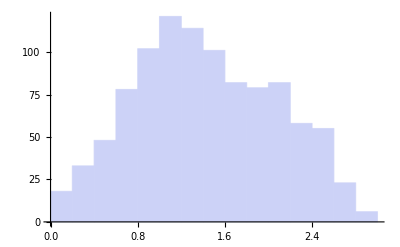

```mathematica
Histogram[rescalingfactor calcI[gFS,points1]]
```

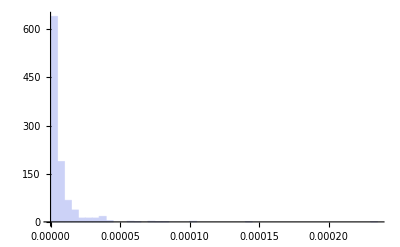

```mathematica
Histogram[rescalingfactor calcI[gmin,points1]]
```